## Orifice

```mathematica
<<C:\\Hopsan\Compgen\CompgenNG.mx
```

```mathematica
path=ToFileName[{"C:","HopsanTrunk","ComponentLibraries","defaultLibrary","Pneumatic"}];
```

```mathematica
domain="Pneumatic";
displayName="Orifice";
brief="Pneumatic orifice";
componentType="ComponentQ";
author="Petter Krus <petter.krus@liu.se>";
affiliation = "Division of Fluid and Mechatronic Systems, Linköping University";
SetFilenames[path,domain,displayName];
ResetComponentVariables[];
Date[]
```

{2014,12,5,17,48,57.1764959}

```mathematica
eps=.
```

```mathematica
inputParameters = {
{Cd,0.65,double,"","Discharge coefficient"},
{R,287.,double,"J/Kg K","Gas constant"},
{cv,718,double,"J/Kg K","heatcoeff"},
{eps,0.02,double,"","Linearisation coeff"}
};
```

```mathematica
inputVariables = {
{A0,1.*10^-6,double,"m2","Area"}
};
```

```mathematica
outputVariables = {
{qma,0.,double,"kg/s","Internal variable"},
{qmb,0.,double,"kg/s","Internal variable"}
};
```

```mathematica
portConnections = {
PneumaticQport[p1,100000.,"fluid port 1",{0,0.5,270}],
PneumaticQport[p2,100000.,"fluid port 2",{1,0.5,90}]
};
```

```mathematica
nodeConnections = {
PneumaticQnode[p1,100000.,"fluid port 1"],
PneumaticQnode[p2,100000.,"fluid port 2"]
};
```

qmp1 = qp1;
qmp2 = qp2;

### The system of equations

The flow at inlet and outlet are equal but with oposit sign.

```mathematica
qmp2=.
```

```mathematica
qmp1e = -qmp2;
```

```mathematica
Ng1=1;
```

```mathematica
qma:=(pp1 Cd A0 Kg Ng)/(√Tp1)
```

```mathematica
qmb:=(pp2 Cd A0 Kg Ng)/(√Tp2)
```

```mathematica
Nga2:= (signedSquareL[((pp2/pp1)^(2/kappa)-(pp2/pp1)^((kappa+1)/kappa))/Ndenom,eps])
```

```mathematica
Ngb2:=(signedSquareL[((pp1/pp2)^(2/kappa)-(pp1/pp2)^((kappa+1)/kappa))/Ndenom,eps])
```

```mathematica
Ng:= onPositive[pp1-pp2](onPositive[pp2/pp1-crit]Nga2 + onNegative[pp2/pp1-crit]Ng1 )+ onNegative[pp1-pp2](onPositive[pp1/pp2-crit]Ngb2 + onNegative[pp1/pp2-crit]Ng1 );
```

### Plotting flow as a function of pressure

#### Parameters

```mathematica
Fa1[qmp2_,pp1_,pp2_]:=qmp2-( onPositive[pp1-pp2] qma - onNegative[pp1-pp2] qmb)
```

```mathematica
keps=1/(-√eps+√(1+eps));
		Kg=√(kappa/R(2/(kappa+1))^((kappa+1)/(kappa-1)));
		Ndenom=(kappa-1)/2(2/(kappa+1))^((kappa+1)/(kappa-1));
		crit=(2/(kappa+1))^(kappa/(kappa-1));
signedSquareL[x_,x0_]:=√(x+x0)-√x0
```

```mathematica
kappa=1+R/cv;
keps=1/(-√eps+√(1+eps));
Kg==√((2^((kappa+1)/(kappa-1))kappa(1/(kappa+1))^((kappa+1)/(kappa-1)))/R);
Ndenom2^((kappa+1)/(kappa-1)-1)(kappa-1)(1/(kappa+1))^((kappa+1)/(kappa-1));
crit=2^(kappa/(kappa-1))(1/(kappa+1))^(kappa/(kappa-1));
```

```mathematica
onPositive[x_]:=(1+Sign[x])/2;
onNegative[x_]:=1-(1+Sign[x])/2;
```

```mathematica
eps =0.001;
kappa = 1.4;
R = 287;
cv = 718;
Cd = 0.65;
A0 = 0.00001;
Tp1=200;
Tp2=200;
pp1 =10^5;
p10=pp1;
p20=pp2;
```

```mathematica
Fa1[qmp2,pp1,pp2]
```

qmp2+1.85771×10^-8 pp2 (1+1/2 (-1-Sign[100000-pp2])) ((1+1/2 (-1-Sign[-(5922339712 (359/1723)^(144/287) 2^(1/287))/5115120067+100000/pp2])+1/2 (-0.0316228+√(0.001+14.9299 (1.3895×10^7 (1/pp2)^1.42857-3.72759×10^8 (1/pp2)^1.71429))) (1+Sign[-(5922339712 (359/1723)^(144/287) 2^(1/287))/5115120067+100000/pp2])) (1+1/2 (-1-Sign[100000-pp2]))+1/2 (1+Sign[100000-pp2]) (1+1/2 (-1-Sign[-(5922339712 (359/1723)^(144/287) 2^(1/287))/5115120067+pp2/100000])+1/2 (-0.0316228+√(0.001+14.9299 (7.19686×10^-8 pp2^1.42857-2.6827×10^-9 pp2^1.71429))) (1+Sign[-(5922339712 (359/1723)^(144/287) 2^(1/287))/5115120067+pp2/100000])))-0.000928855 (1+Sign[100000-pp2]) ((1+1/2 (-1-Sign[-(5922339712 (359/1723)^(144/287) 2^(1/287))/5115120067+100000/pp2])+1/2 (-0.0316228+√(0.001+14.9299 (1.3895×10^7 (1/pp2)^1.42857-3.72759×10^8 (1/pp2)^1.71429))) (1+Sign[-(5922339712 (359/1723)^(144/287) 2^(1/287))/5115120067+100000/pp2])) (1+1/2 (-1-Sign[100000-pp2]))+1/2 (1+Sign[100000-pp2]) (1+1/2 (-1-Sign[-(5922339712 (359/1723)^(144/287) 2^(1/287))/5115120067+pp2/100000])+1/2 (-0.0316228+√(0.001+14.9299 (7.19686×10^-8 pp2^1.42857-2.6827×10^-9 pp2^1.71429))) (1+Sign[-(5922339712 (359/1723)^(144/287) 2^(1/287))/5115120067+pp2/100000])))

```mathematica
AFa1[pp1_,pp2_]:= qmp2/.FindRoot[Fa1[qmp2,pp1,pp2]==0,{qmp2,2}]
```

```mathematica
pp2=.
```

```mathematica
crit
```

(5922339712 (359/1723)^(144/287) 2^(1/287))/5115120067

```mathematica
Ng
```

(1+1/2 (-1-Sign[-(5922339712 (359/1723)^(144/287) 2^(1/287))/5115120067+100000/pp2])+1/2 (-0.0316228+√(0.001+14.9299 (1.3895×10^7 (1/pp2)^1.42857-3.72759×10^8 (1/pp2)^1.71429))) (1+Sign[-(5922339712 (359/1723)^(144/287) 2^(1/287))/5115120067+100000/pp2])) (1+1/2 (-1-Sign[100000-pp2]))+1/2 (1+Sign[100000-pp2]) (1+1/2 (-1-Sign[-(5922339712 (359/1723)^(144/287) 2^(1/287))/5115120067+pp2/100000])+1/2 (-0.0316228+√(0.001+14.9299 (7.19686×10^-8 pp2^1.42857-2.6827×10^-9 pp2^1.71429))) (1+Sign[-(5922339712 (359/1723)^(144/287) 2^(1/287))/5115120067+pp2/100000]))

```mathematica
p10=pp1;
p20=pp2;
```

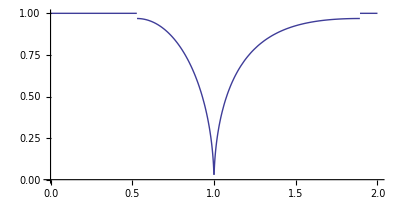

```mathematica
ParametricPlot[{pp2/pp1,Ng},{pp2,1,200000}]
```

```mathematica
qma
```

0.00185771 ((1+1/2 (-1-Sign[-(5922339712 (359/1723)^(144/287) 2^(1/287))/5115120067+100000/pp2])+1/2 (-0.0316228+√(0.001+14.9299 (1.3895×10^7 (1/pp2)^1.42857-3.72759×10^8 (1/pp2)^1.71429))) (1+Sign[-(5922339712 (359/1723)^(144/287) 2^(1/287))/5115120067+100000/pp2])) (1+1/2 (-1-Sign[100000-pp2]))+1/2 (1+Sign[100000-pp2]) (1+1/2 (-1-Sign[-(5922339712 (359/1723)^(144/287) 2^(1/287))/5115120067+pp2/100000])+1/2 (-0.0316228+√(0.001+14.9299 (7.19686×10^-8 pp2^1.42857-2.6827×10^-9 pp2^1.71429))) (1+Sign[-(5922339712 (359/1723)^(144/287) 2^(1/287))/5115120067+pp2/100000])))

```mathematica
Tp1
```

200

```mathematica
qmp2 =.
```

```mathematica
nmax=300;
qmlist=Array[a1,nmax];
qmdlist=Array[a2,{nmax,2}];
```

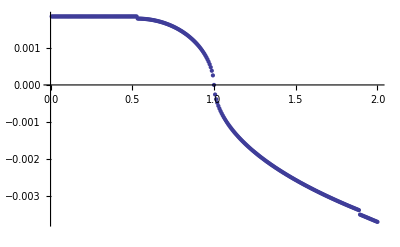

```mathematica
For[i=1,i<nmax+1,i++,
	pp2 = pp1 2 i/nmax;
	qmdlist[[i]]={pp2/pp1,AFa1[pp1,pp2]}
];
ListPlot[qmdlist]
```

```mathematica
eps =.;
kappa =.;
R = .;
cv = .;
Cd = .;
A0=.;
Tp1=.;
Tp2=.;
pp1=.;
pp2=.;
p10=.;
p20=.;
qma=.;
qmb=.;
```

```mathematica
keps=.;
Kg=.;
Ndenom=.;
crit=.;
onPositive[x_]=.;
onNegative[x_]=.;
signedSquareL[x_,x0_]=.;
```

### Equations

Calculation of parameters

Kg==√(kappa/R(2/(kappa+1))^((kappa+1)/(kappa-1)))

Ndenom==(kappa-1)/2(2/(kappa+1))^((kappa+1)/(kappa-1))

crit==(2/(kappa+1))^(kappa/(kappa-1))

```mathematica
localExpressions ={
kappa==1+R/cv,
keps==1/(-√eps+√(1+eps)),
Kg==√((2^((kappa+1)/(kappa-1))kappa(1/(kappa+1))^((kappa+1)/(kappa-1)))/R),
Ndenom==2^((kappa+1)/(kappa-1)-1)(kappa-1)(1/(kappa+1))^((kappa+1)/(kappa-1)),
crit==2^(kappa/(kappa-1))(1/(kappa+1))^(kappa/(kappa-1)),
cp==cv+R
};
```

```mathematica
systemEquationsDA=Simplify[{
qmp2==(onPositive[pp1-pp2] qma - onNegative[pp1-pp2] qmb),
dEp1==qmp1e cp(onNegative[qmp1e] Tp1+onPositive[qmp1e] Tp2),
dEp2==qmp2 cp(onNegative[qmp2] Tp2+onPositive[qmp2] Tp1)
	}];
```

```mathematica
systemEquationsDA=Simplify[{
qma==(pp1 Cd A0 Kg Ng)/(√Tp1),
qmb==(pp2 Cd A0 Kg Ng)/(√Tp2),
qmp2==(onPositive[pp1-pp2] qma - onNegative[pp1-pp2] qmb),
dEp1==qmp1e cp(onNegative[qmp1e] Tp1+onPositive[qmp1e] Tp2),
dEp2==qmp2 cp(onNegative[qmp2] Tp2+onPositive[qmp2] Tp1)
	}];
```

```mathematica
Unprotect["Power"];
onPositive[x_]^2:=1;
```

```mathematica
systemVariables = {qma,qmb,qmp2,dEp1,dEp2,pp1,pp2};
```

### Boundarys

```mathematica
systemBoundaryEquations = { 
pp1 == (cp1 + Zcp1 dEp1 ),
pp2 ==(cp2 + Zcp2 dEp2 )
};
```

### Expressions

The inlet flow is calculated as the outlet flow with reversed sign.

```mathematica
expressions = {
qmp1==-qmp2
};
```

Initial values

```mathematica
systemEquationsDA
```

{qma==1/(√Tp1)A0 Cd Kg pp1 (onNegative[pp1-pp2] (onNegative[-crit+pp1/pp2]+onPositive[-crit+pp1/pp2] signedSquareL[(-(pp1/pp2)^(1+1/kappa)+(pp1/pp2)^(2/kappa))/Ndenom,eps])+onPositive[pp1-pp2] (onNegative[-crit+pp2/pp1]+onPositive[-crit+pp2/pp1] signedSquareL[(-(pp2/pp1)^(1+1/kappa)+(pp2/pp1)^(2/kappa))/Ndenom,eps])),qmb==1/(√Tp2)A0 Cd Kg pp2 (onNegative[pp1-pp2] (onNegative[-crit+pp1/pp2]+onPositive[-crit+pp1/pp2] signedSquareL[(-(pp1/pp2)^(1+1/kappa)+(pp1/pp2)^(2/kappa))/Ndenom,eps])+onPositive[pp1-pp2] (onNegative[-crit+pp2/pp1]+onPositive[-crit+pp2/pp1] signedSquareL[(-(pp2/pp1)^(1+1/kappa)+(pp2/pp1)^(2/kappa))/Ndenom,eps])),qmp2+qmb onNegative[pp1-pp2]==qma onPositive[pp1-pp2],dEp1+cp qmp2 Tp1 onNegative[-qmp2]+cp qmp2 Tp2 onPositive[-qmp2]==0,dEp2==cp qmp2 (Tp2 onNegative[qmp2]+Tp1 onPositive[qmp2])}

```mathematica
cp1/.Solve[systemBoundaryEquations,{cp1,cp2}][[1]]
```

pp1-dEp1 Zcp1

```mathematica
Compgen[file]
```

XMLElement::cntsList: XMLElement["modelobject", {"typename" → "PneumaticOrifice", "displayname" → "PneumaticOrifice"}, {XMLElement["icon", {"isopath" → "PneumaticOrifice.svg", "iconrotation" → "ON", "userpath" → "PneumaticOrifice.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.333333, "a" → "0", "name" → "Pp1"}, {}], XMLElement["portpose", {"x" → "0", "y" → 0.666667, "a" → "0", "name" → "Pp2"}, {}], XMLElement["portpose", {"x" → 0.5, "y" → "0", "a" → "270", "name" → "A0"}, {}], XMLElement["portpose", {"x" → "0.333333", "y" → "1", "a" → "90", "name" → "qma"}, {}], XMLElement["portpose", {"x" → "0.666667", "y" → "1", "a" → "90", "name" → "qmb"}, {}]}]}] in XMLElement["hopsanobjectappearance", {"version" → "0.1"}, XMLElement["modelobject", {"typename" → "PneumaticOrifice", "displayname" → "PneumaticOrifice"}, {XMLElement["icon", {"isopath" → "PneumaticOrifice.svg", "iconrotation" → "ON", "userpath" → "PneumaticOrifice.svg"}, {}], XMLElement["portpositions", {}, {XMLElement["portpose", {"x" → "0", "y" → 0.333333, "a" → "0", "name" → "Pp1"}, {}], XMLElement["portpose", {"x" → "0", "y" → 0.666667, "a" → "0", "name" → "Pp2"}, {}], XMLElement["portpose", {"x" → 0.5, "y" → "0", "a" → "270", "name" → "A0"}, {}], XMLElement["portpose", {"x" → "0.333333", "y" → "1", "a" → "90", "name" → "qma"}, {}], XMLElement["portpose", {"x" → "0.666667", "y" → "1", "a" → "90", "name" → "qmb"}, {}]}]}]] is not a list of contents. The third item in an XMLElement must be a list of contents, even if it is an empty list.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.333333 in "y" → 0.333333 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

XMLElement::attrhs: 0.666667 in "y" → 0.666667 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

Export::autofix: Malformed symbolic XML expression encountered. This may result in unexpected XML data.

General::stop: Further output of Export :: autofix will be suppressed during this calculation.

XMLElement::attrhs: 0.5 in "x" → 0.5 is not a valid value for an attribute in an XMLElement. The value of the attribute must be a string.

General::stop: Further output of XMLElement :: attrhs will be suppressed during this calculation.

```mathematica
*
```

```mathematica
*
```